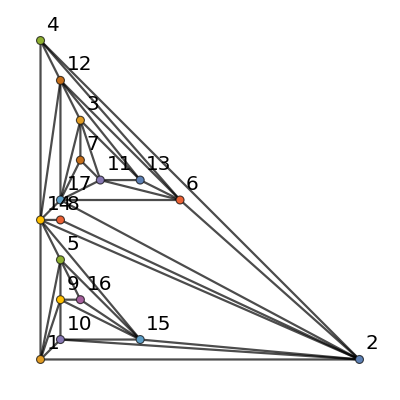

t1_1.eps

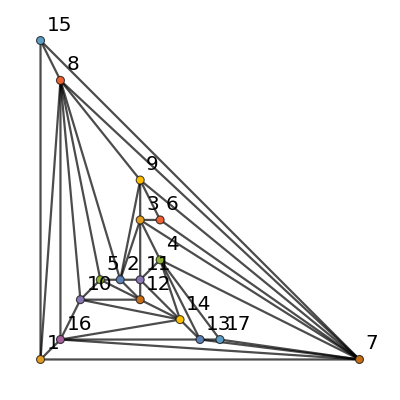

t1_2.eps

```mathematica
G[1]=System`Graph[{1<->2,1<->5,1<->9,1<->10,1<->14,2<->4,2<->6,2<->8,2<->10,2<->14,2<->15,2<->17,3<->7,3<->11,3<->12,3<->13,3<->17,4<->6,4<->12,4<->14,5<->9,5<->14,5<->15,5<->16,6<->11,6<->12,6<->13,6<->17,7<->11,7<->17,8<->14,9<->10,9<->15,9<->16,10<->15,11<->13,11<->17,12<->13,12<->14,12<->17,14<->15,14<->17,15<->16},GraphLayout->"PlanarEmbedding",VertexLabels->"Name",System`VertexStyle->Thread[{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17}->(ColorData[97]/@{2,1,2,3,3,4,6,4,8,5,5,6,1,8,7,9,7})],VertexSize->0.4,VertexLabelStyle->Directive[Black,20],EdgeStyle->{{Thickness[0.004],Black}}]
Export["t1_1.eps",G[1]]

G[2]=System`Graph[{1<->7,1<->8,1<->15,1<->16,2<->3,2<->5,2<->8,2<->9,2<->11,2<->12,3<->4,3<->6,3<->7,3<->9,3<->11,4<->7,4<->11,4<->13,4<->14,4<->17,5<->8,5<->10,5<->12,6<->7,6<->9,7<->8,7<->9,7<->13,7<->15,7<->16,7<->17,8<->9,8<->10,8<->15,8<->16,10<->12,10<->14,10<->16,11<->12,11<->14,12<->14,13<->14,13<->16,13<->17,14<->16},GraphLayout->"PlanarEmbedding",VertexLabels->"Name",System`VertexStyle->Thread[{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17}->(ColorData[97]/@{2,1,2,3,3,4,6,4,8,5,5,6,1,8,7,9,7})],VertexSize->0.4,VertexLabelStyle->Directive[Black,20],EdgeStyle->{{Thickness[0.004],Black}}]
Export["t1_2.eps",G[2]]
```

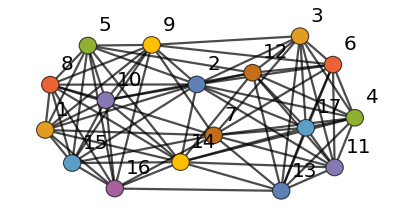

-Graphics-

-Graphics-

```mathematica
mvc={2,1,2,3,3,4,6,4,8,5,5,6,1,8,7,9,7};
GUNION=GraphUnion[G[1],G[2],VertexLabels->"Name",VertexSize->0.4,VertexLabelStyle->Directive[Black,20],EdgeStyle->{{Thickness[0.004],Black}}];
GUNIONCOLORED=SetProperty[GUNION,System`VertexStyle->Thread[System`VertexList[GUNION]->(ColorData[97]/@mvc)]]
G[1]=SetProperty[G[1],System`VertexStyle->Thread[System`VertexList[GUNION]->(ColorData[97]/@mvc)]]
G[2]=SetProperty[G[2],System`VertexStyle->Thread[System`VertexList[GUNION]->(ColorData[97]/@mvc)]]
```